```mathematica
242.9/1.5
```

161.933

```mathematica
D=2
```

Set::wrsym: Symbol D is Protected.

2

```mathematica
Clear[y0,p,y,v]
y0[imp_,ϕ_, i_] = imp * Sin[ϕ*π/180.]/Cos[i * π/180.];
y[Dlos_,i_,ϕ_,imp_]=Dlos*Sin[i*π/180.]+y0[imp,ϕ,i];
p[imp_,ϕ_] = imp * Cos[ϕ*π/180.];
```

```mathematica
vexp[v_,i_,hv_,imp_,ϕ_,Dlos_]=
(-v*Sin[i*π/180.])/(√(1 +  (y[Dlos,i,ϕ,imp]/p[imp,ϕ])^2))Exp[(-Abs[y[Dlos,i,ϕ,imp] - y0[imp, ϕ,i]])/(hv Tan[i*π/180.])];
```

```mathematica
vsimple[v_,i_,hv_,imp_,ϕ_,Dlos_]=(-v*Sin[i*π/180.])/(√(1 +  (y[Dlos,i,ϕ,imp]/p[imp,ϕ])^2));
```

```mathematica
vmax = 232.286425223;
```

```mathematica
vexp[177.659,80.,1000.,342.94,88.0,1995.3237]
```

-0.375961

```mathematica
vsimple[vmax,85.,24.599,26.109,0,0]
```

-231.403

```mathematica
Manipulate[Plot[vexp[177,80.,1000.,342.94,az,dlos],{dlos,-600,2000},PlotRange->All],{az,0,90}]
```

```mathematica
Manipulate[Plot[vexp[177,i,hv,342.94,88.0,dlos],{dlos,-600,2000},PlotRange->All],{hv,0.1, 2000},{i,-90.,90}]
```

## NFW

```mathematica
Clear[x,top,bottom,vr]
x[r_,r200_] =r/r200;
```

```mathematica
vr[v200_,c_,r_,r200_] := v200*Sqrt[(Log[1+c*x[r,r200]] - (c*x[r,r200])/(1+c*x[r,r200]))/(x[r,r200]*(Log[1+c] - c/(1+c)))];
```

```mathematica
top[8,25,180]//N
```

top[8.,25.,180.]

```mathematica
vr[150,8,25,180]
```

180 √((5 (-10/19+Log[19/9]))/(-8/9+Log[9]))

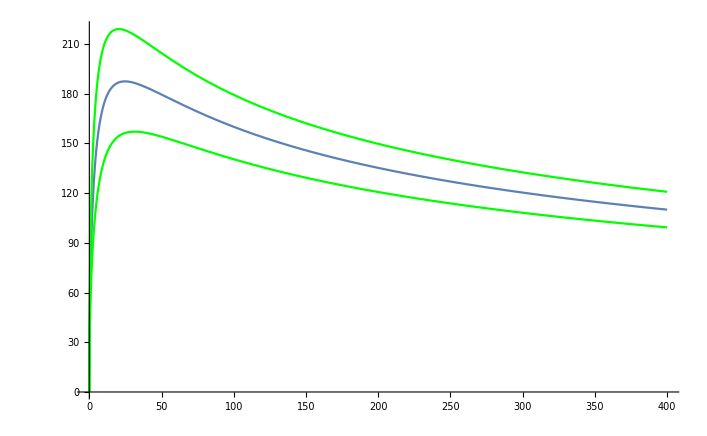

```mathematica
Show[Plot[vr[125.7,22.7,r,258.9],{r,0,400},PlotRange->All],
Plot[vr[125.7+13,22.7+4.8,r,258.9],{r,0,400},PlotRange->All,PlotStyle->Green],
Plot[vr[125.7-13,22.7-4.8,r,258.9],{r,0,400},PlotRange->All,PlotStyle->Green]]
```

```mathematica
Manipulate[Plot[vr[v200,c,r,r200],{r,0,400},PlotRange->All],{c,1, 45},{v200,50,200},{r200,50,250}]
```

```mathematica
195/1.2
```

162.5

```mathematica
f[z_]=Log[z+1]-z
```

-z+Log[1+z]

```mathematica
f[1]
```

-1+Log[2]

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

```mathematica
13/38.
```

0.342105